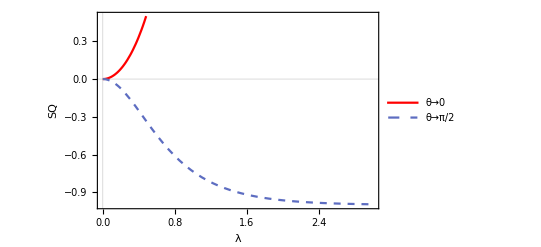

Export::chtype: 第一个参数 … 不是一个有效的文件指定.

$Failed

```mathematica
ClearAll;
ClearAll["`*", Subscript, Derivative];
ClearAll["Global`*",Derivative,Subscript];
SQFF=(2(Re[ ⅇ^(-2ⅈ θ) Subscript[F, 2]]-2 Re[ ⅇ^(-ⅈ θ) Subscript[F, 1] ]^2+Subscript[F, 3]))/(2 Sinh[λ]^2+1);
Subscript[F, 1]=1/2 Sinh[2λ];
Subscript[F, 2]=1/2 Sinh[2λ]^2;
Subscript[F, 3]=1/4 Sinh[2λ]^2+Sinh[λ]^4;
range={0,π/2};
a=Plot[Evaluate[SQFF/.{θ->range}],{λ,0,3},PlotRange->{-1,0.5},PlotTheme->"Scientific",PlotStyle->{Red,Dashed},PlotLegends->Placed[StringForm["θ→``",#]&/@range,{Right,Top}],FrameLabel->{"λ","SQ"},PlotRange->Full,Frame->True]
Export[a,"PNG","C:\\Users\\Lenovo\\Desktop\\Fig"]
```